## Практическое задание №3 Дунаев Виктор Андреевич 3 Курс, 6 Группа

## Задание 1

```mathematica
(* Инициализация чисел *)
c1 = 4+ 3I
```

4+3 ⅈ

```mathematica
c2 =Complex[Sqrt[5], 1]
```

Complex[√5,1]

```mathematica
c3 = 2.3 +4.0I
```

2.3+4. ⅈ

```mathematica
c4 = 7/6 - 4/I
```

7/6+4 ⅈ

```mathematica
(* функции Re Im Abs *)
myAbs[Complex[x_, y_]] := Sqrt[x x+y y]
```

```mathematica
myAbs[c1]
```

5

```mathematica
myRe [Complex[x_, y_]] := x
```

```mathematica
myRe[c1]
```

4

```mathematica
Re[c1]
```

4

```mathematica
myIm [Complex[x_, y_]] := y
```

```mathematica
myIm[c1]
```

3

```mathematica
Im[c1]
```

3

```mathematica
(* угол наклона радиус-вектора *)
myArg[Complex[x_, y_]] := ArcTan[y/x]
```

```mathematica
myArg[c1]
```

ArcTan[3/4]

```mathematica
Arg[c1]
```

ArcTan[3/4]

```mathematica
(* Комплексно сопряженные числа *)
myConjugate[x_Complex] := 2Re[x]-x
```

```mathematica
myConjugate[c1]
```

4-3 ⅈ

```mathematica
Conjugate[c1]
```

4-3 ⅈ

## Задание 2

```mathematica
number = 28.04
```

28.04

```mathematica
BaseForm[number,2]
```

11100.000010100011111_2

```mathematica
BaseForm[number,19]
```

(19.0e8)_19

## Задание 3

```mathematica
num = 28041998
```

28041998

```mathematica
newList = {}
```

{}

```mathematica
Do[AppendTo[newList, IntegerPart[Mod[num,10^i]/(10^(i-1))]],{i, 8}]
```

```mathematica
newList
```

{8,9,9,1,4,0,8,2}

```mathematica
Reverse[newList]
```

{2,8,0,4,1,9,9,8}

```mathematica
BaseForm[newList, 9]
```

{8_9,10_9,10_9,1_9,4_9,0_9,8_9,2_9}

```mathematica
BaseForm[newList, 40]
```

BaseForm::basf: Requested base 40 should be an integer between 2 and 36.

BaseForm[{8,9,9,1,4,0,8,2},40]

## Задание 4

```mathematica
Table[ RandomInteger[{-1,1}]*7, RandomInteger[{7,11}]]
```

{0,7,-7,-7,7,7,0,0}

```mathematica
Table[ 7 - RandomInteger[1]*14, RandomInteger[{7,11}]]
```

{-7,-7,-7,-7,-7,-7,-7,7,-7,7}

```mathematica
Table[ FromCharacterCode[RandomInteger[{97, 99}]], RandomInteger[{7,11}]]
```

{c,b,b,c,a,a,b}

```mathematica
Table[ RandomChoice[{RandomReal[],RandomInteger[{2, 45}]}], RandomInteger[{7,11}]]
```

{22,0.684406,0.579556,44,15,45,0.182315,28,0.306915,8,0.128129}

## Задание 5

```mathematica
expr = N[ⅇ^Pi, 30]
```

23.1406926327792690057290863679

```mathematica
Reduce[1/expr*m ≥ 10^-5, m]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

m≥0.000231406926327792690057290863679

```mathematica
Reduce[1/expr*m < 10, m]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

m<231.406926327792690057290863679

```mathematica
Reduce[1/expr*m < 10^5, m]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

m<2.31406926327792690057290863679×10^6

## Задание 6

```mathematica
newList1 = {2,8,0,4,1,9,9,8}
```

{2,8,0,4,1,9,9,8}

```mathematica
s = SparseArray[{{i_,j_}/; i-j==1-> 99,{i_,j_}/; i-j==-1-> 55,{i_,i_}->newList1⟦i⟧},{8,8},77]
```

Part::pkspec1: The expression i cannot be used as a part specification.

SparseArray[<22>, {8, 8}, 77]

```mathematica
MatrixForm[s]
```

(2 | 55 | 77 | 77 | 77 | 77 | 77 | 77
99 | 8 | 55 | 77 | 77 | 77 | 77 | 77
77 | 99 | 0 | 55 | 77 | 77 | 77 | 77
77 | 77 | 99 | 4 | 55 | 77 | 77 | 77
77 | 77 | 77 | 99 | 1 | 55 | 77 | 77
77 | 77 | 77 | 77 | 99 | 9 | 55 | 77
77 | 77 | 77 | 77 | 77 | 99 | 9 | 55
77 | 77 | 77 | 77 | 77 | 77 | 99 | 8)

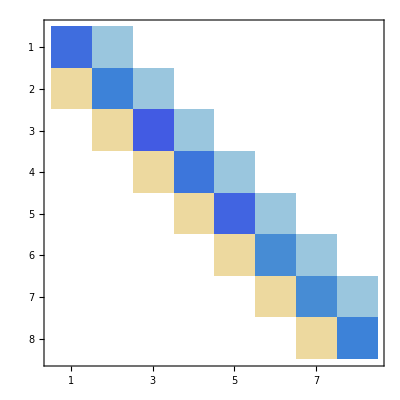

```mathematica
MatrixPlot[s]
```

## Задание 7

```mathematica
(* 6.2 -> 9 и наоборот *)
Round[6.2, 9]
```

9

```mathematica
Round[9,6.2]
```

6.2

```mathematica
(* для 5.25 и 8.5 *)
Round[5.25, 9]
```

9

```mathematica
Round[9, 8.5]
```

8.5

```mathematica
(* для 8.5 и 5.25 *)
```

```mathematica
Round[8.5,9]
Floor[9,5.25]
```

9

5.25